```mathematica
Quit[];
```

```mathematica
SetDirectory["~/Documents/Univ/phase_space_stoc/git/num/AndoVennin"]
```

/Users/yuichirotada/Documents/Univ/phase_space_stoc/git/num/AndoVennin

### double chaotic SR

```mathematica
model="double_chaotic";
```

```mathematica
fndata=Import[model<>"/Mn_"<>model<>"_SR.dat"];
trajdata=Import[model<>"/traj_"<>model<>"_SR.dat"];
calPdata=Import[model<>"/calP_"<>model<>"_SR.dat"];
```

```mathematica
f1List=Table[{fndata[[i,1]],fndata[[i,2]],fndata[[i,3]]},{i,1,Length[fndata],5}];
g2List=Table[{fndata[[i,1]],fndata[[i,2]],Log10[fndata[[i,4]]]},{i,1,Length[fndata],5}];
phivschi=Table[{trajdata[[i,2]],trajdata[[i,3]]},{i,Length[trajdata]}];
meancalP=Table[{calPdata[[i,1]],calPdata[[i,2]]±calPdata[[i,3]]},{i,Length[calPdata]}];
```

```mathematica
Show[ListContourPlot[f1List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/N.pdf",Show[ListContourPlot[f1List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->BarLegend[Automatic,LegendLabel->⟨𝒩⟩]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]];
```

```mathematica
Show[ListContourPlot[g2List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/dN2.pdf",Show[ListContourPlot[g2List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]];
```

```mathematica
dynfile=Import["../../../c++/output/doublechaotic_dyn.dat"];
calPcpp=Import["../../../c++/output/doublechaotic_spec.dat"];
```

```mathematica
aHList=Table[{dynfile[[i,1]],dynfile[[i,5]]},{i,Length[dynfile]}];
```

```mathematica
Nf=Last[aHList][[1]]
```

86.08

```mathematica
calPint=Interpolation[calPcpp];
```

```mathematica
calPcppvsN=Table[{Nf-aHList[[i,1]],calPint[aHList[[i,2]]]},{i,Length[aHList]}];
```

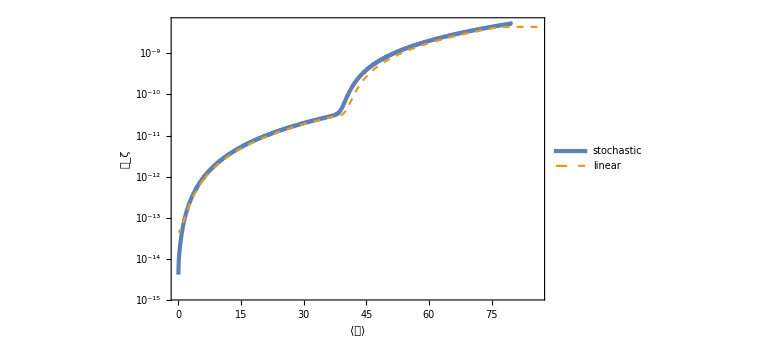

```mathematica
ListLogPlot[{meancalP,calPcppvsN},FrameLabel->{⟨𝒩⟩,Subscript[𝒫, ζ]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{"stochastic","linear"},LabelStyle->Directive[Larger,Black,FontFamily->"Optima"]],{0.8,0.2}]]
```

### hybrid SR

```mathematica
model="hybrid";
```

```mathematica
Sample=Import[model<>"/sample_"<>model<>"_SR.dat"];
```

```mathematica
phiSample=Table[{Sample[[i,1]],Sample[[i,2]]},{i,Length[Sample]}];
psiSample=Table[{Sample[[i,1]],Sample[[i,3]]},{i,Length[Sample]}];
VSample=Table[{Sample[[i,1]],Sample[[i,4]]},{i,Length[Sample]}];
```

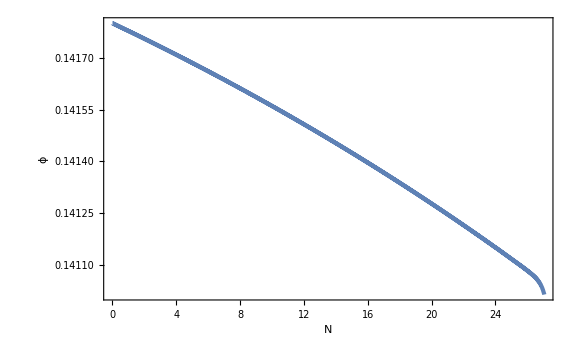

```mathematica
ListPlot[phiSample,FrameLabel->{N,ϕ}]
```

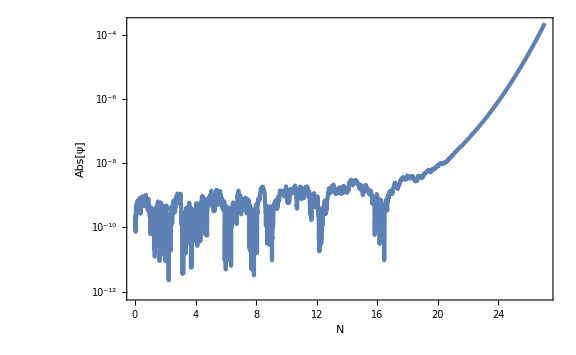

```mathematica
ListLogPlot[Abs[psiSample],FrameLabel->{N,Abs[ψ]}]
```

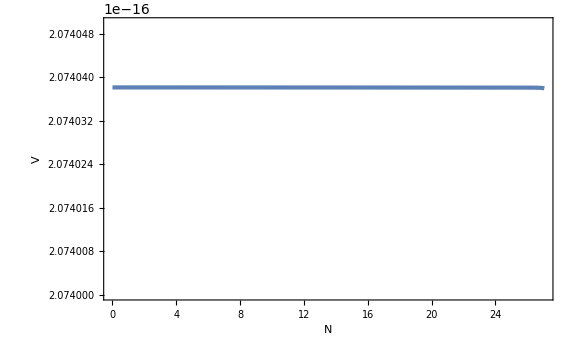

```mathematica
ListPlot[VSample,FrameLabel->{N,V},PlotRange->{2.074 10^-16,2.07405 10^-16}]
```

```mathematica
fndata=Sort[Select[Import[model<>"/Mn_"<>model<>"_SR.dat"],#[[2]]>0&]];
trajdata=Import[model<>"/traj_"<>model<>"_SR.dat"];
calPdata=Import[model<>"/calP_"<>model<>"_SR.dat"];
```

```mathematica
Last[trajdata]
```

{27.123,0.141013,0.000224644,0.00193687,1.18218×10^-14}

```mathematica
datared=1;
```

```mathematica
f1List=Table[{fndata[[i,1]],Log10[fndata[[i,2]]],fndata[[i,3]]},{i,1,Length[fndata],datared}];
g2List=Table[{fndata[[i,1]],Log10[fndata[[i,2]]],Log10[fndata[[i,4]]]},{i,1,Length[fndata],datared}];
phivschi=Table[{trajdata[[i,2]],Log10[Abs[trajdata[[i,3]]]]},{i,Length[trajdata]}];
Ndata=Table[{trajdata[[i,1]],trajdata[[i,4]]},{i,Length[trajdata]}];
dN2data=Table[{trajdata[[i,1]],trajdata[[i,5]]},{i,Length[trajdata]}];
meandN2=Table[{calPdata[[i,1]],calPdata[[i,2]]},{i,Length[calPdata]}];
meancalP=Table[{calPdata[[i,1]],calPdata[[i,2]]±calPdata[[i,3]]},{i,Length[calPdata]}];
```

```mathematica
Ncontour=Show[ListContourPlot[f1List,FrameLabel->{"ϕ/M_Pl","log_10(|ψ|/M_Pl)"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio,Contours->{{0,{Thick,Dotted}},2,5,10,15,20,25,30,35}],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/N.pdf",Ncontour];
```

```mathematica
dN2contour=Show[ListContourPlot[g2List,FrameLabel->{"ϕ/M_Pl","log_10(|ψ|/M_Pl)"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/dN2.pdf",dN2contour];
```

```mathematica
As=2.189 10^-9;
Π2=50;
M=0.1;
ϕc=0.1Sqrt[2];
μ2=11;
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

35355.3

2.07404×10^-16

```mathematica
ψ0=Sqrt[(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0)]
```

1.96975×10^-9

10.835

```mathematica
N1=(Sqrt[χ2]M ϕc^(1/2)μ1^(1/2))/2
N2=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2])
```

11.6378

0.537044

```mathematica
ξk[NN_]=-(N1+N2-NN)/(ϕc μ1);
χk[NN_]=(4ϕc μ1 ξk[NN]^2)/M^2;
ψk[NN_]=ψ0 Exp[χk[NN]];
```

```mathematica
calPCG[NN_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2 ψk[NN]^2);
```

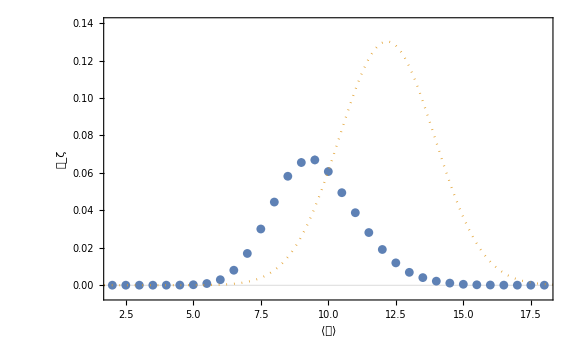

```mathematica
Show[ListPlot[meancalP,FrameLabel->{⟨𝒩⟩,Subscript[𝒫, ζ]},PlotRange->{{2,18},{-0.005,0.14}},GridLines->{None,{0}},Joined->False,IntervalMarkers->"Fences"],Plot[calPCG[NN],{NN,0,28},PlotStyle->{Color[2],Dotted}]]
```

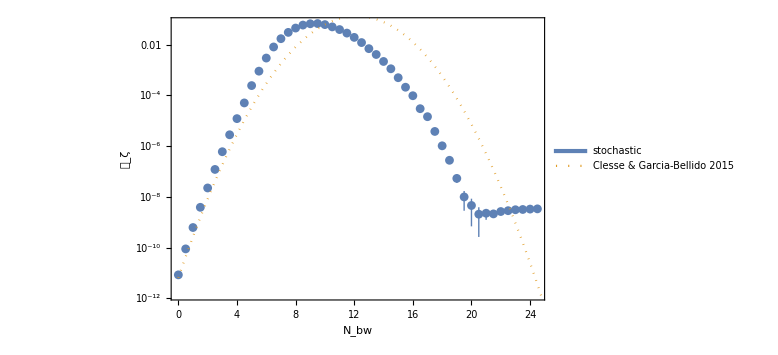

```mathematica
Show[ListLogPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},Joined->False,IntervalMarkers->"Fences"],LogPlot[{0,calPCG[NN]},{NN,0,28},PlotStyle->{AbsoluteThickness[3],Dotted},PlotLegends->Placed[LineLegend[{"stochastic","Clesse & Garcia-Bellido 2015"},LabelStyle->Directive[Larger,Black,FontFamily->"Optima"]],{0.38,0.15}]]]
```